```mathematica
(* Image Processing - Find Dangling Ends *)

(* Import image *)
img=Import["/Users/jgoddy/Library/Mobile Documents/com~apple~CloudDocs/Documents/Barmak_research/grain_unet/Closing_Dangling_boundaries/segmentationexample.png","PNG"]
```

-Graphics-

```mathematica
data=ImageData[Binarize[img]];  (* Binarize the image. *)
Dimensions[data]  (* Image dimensions *)
```

{512,512}

```mathematica
Print["Number of pixels: ",Length[Position[Round[data],0]]];  (* Print the number of boundary pixels *)
Print["List of boundary pixels."];
listofpixels=Position[Round[data],0]  (* List of boundary pixels *)
```

Number of pixels: 9368

List of boundary pixels.

```mathematica
(* Find endpoints of dangling segments *)
dangle={};
Do[
near=Nearest[Delete[listofpixels,i],listofpixels[[i]],{All,Sqrt[2]}];If[Length[near]==1&&listofpixels[[i,1]]!=1&&listofpixels[[i,2]]!=1&&listofpixels[[i,1]]!=512&&listofpixels[[i,2]]!=512,AppendTo[dangle,listofpixels[[i]]]],{i,1,Length[listofpixels]}]
```

```mathematica
Print["List of dangling pixels"];
dangle
```

List of dangling pixels

{{4,80},{36,345},{76,496},{116,216},{186,491},{196,365},{213,505},{220,41},{237,345},{286,38},{294,435},{299,382},{311,101},{316,431},{335,70},{383,505},{412,368},{415,404},{440,406},{476,123},{489,410},{510,421},{510,509}}

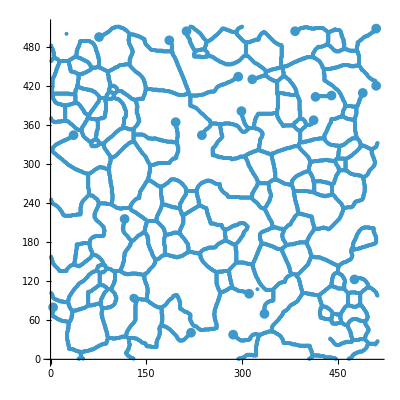

```mathematica
(* Plot of segmented microstructure and dangling pixels. *)
Show[ListPlot[{listofpixels},PlotMarkers->{{Automatic,Tiny}},AspectRatio->1],ListPlot[{dangle},PlotMarkers->{{Automatic,Medium}},AspectRatio->1]]
```

```mathematica
dangle
```

{{4,80},{36,345},{76,496},{116,216},{186,491},{196,365},{213,505},{220,41},{237,345},{286,38},{294,435},{299,382},{311,101},{316,431},{335,70},{383,505},{412,368},{415,404},{440,406},{476,123},{489,410},{510,421},{510,509}}

```mathematica
dangle[[3]]
```

{76,496}

```mathematica
dangle
```

{{4,80},{36,345},{76,496},{116,216},{186,491},{196,365},{213,505},{220,41},{237,345},{286,38},{294,435},{299,382},{311,101},{316,431},{335,70},{383,505},{412,368},{415,404},{440,406},{476,123},{489,410},{510,421},{510,509}}

```mathematica
Nearest[listofpixels,dangle[[3]],{15,15}]
```

{{76,496},{77,496},{78,497},{79,497},{80,498},{81,498},{82,499},{83,499},{84,500},{85,501},{86,501},{87,502},{88,502},{66,487},{67,486}}

```mathematica
Nearest[listofpixels,dangle[[3]],{13,15}]
```

{{76,496},{77,496},{78,497},{79,497},{80,498},{81,498},{82,499},{83,499},{84,500},{85,501},{86,501},{87,502},{88,502}}

```mathematica
Nearest[listofpixels,dangle[[3]],{14,15}]
```

{{76,496},{77,496},{78,497},{79,497},{80,498},{81,498},{82,499},{83,499},{84,500},{85,501},{86,501},{87,502},{88,502},{66,487}}

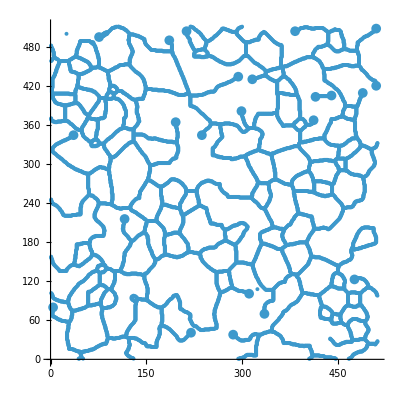

```mathematica
Show[ListPlot[{listofpixels},PlotMarkers->{{Automatic,Tiny}},AspectRatio->1],ListPlot[{dangle},PlotMarkers->{{Automatic,Medium}},AspectRatio->1],
ListPlot[{Nearest[listofpixels,dangle[[3]],{14,15}]}, PlotMarkers->{Red, Medium,"OpenMarkers"},AspectRatio->1]]
```

```mathematica
p=Predict[dangle,Method->"NearestNeighbors"]
```

Predict::mlbddataev: The data being evaluated is not formatted correctly.

Predict[{{4,80},{36,345},{76,496},{116,216},{186,491},{196,365},{213,505},{220,41},{237,345},{286,38},{294,435},{299,382},{311,101},{316,431},{335,70},{383,505},{412,368},{415,404},{440,406},{476,123},{489,410},{510,421},{510,509}},Method→NearestNeighbors]

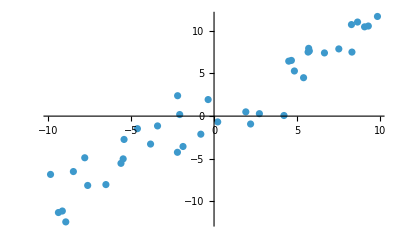

{8.26867→10.721,-2.20244→-4.23723,-2.06661→0.186026,4.83489→5.28664,-7.77941→-4.87851,4.65447→6.52262,-9.36376→-11.2926,9.05797→10.4577,8.29821→7.50101,0.220563→-0.67822,4.20872→0.071902,-9.12913→-11.1143,-4.61026→-1.4692,4.49515→6.43768,-3.81949→-3.27208,-8.92124→-12.3891,1.91183→0.49796,-6.50687→-8.01856,-5.59987→-5.53049,9.28362→10.5529,5.65975→7.50152,2.72913→0.287327,-1.86694→-3.55745,9.83363→11.6728,-5.41449→-2.73163,-2.19177→2.39006,5.73349→7.62933,7.50821→7.87137,-9.83809→-6.8284,-0.355111→1.93936,-7.60303→-8.12003,8.63509→11.0196,6.64389→7.40188,-0.794894→-2.11547,-8.46349→-6.49192,5.69377→7.9362,-3.39959→-1.1482,5.38727→4.49883,2.19951→-0.922955,-5.46792→-5.00687}

```mathematica
data=Table[x->x+RandomVariate[NormalDistribution[0, 2]], {x, RandomReal[{-10, 10}, 40]}];
ListPlot[List@@@data]
```

```mathematica
p=Predict[data,Method->"NearestNeighbors"]
```

PredictorFunction[…]

```mathematica
p=.
```

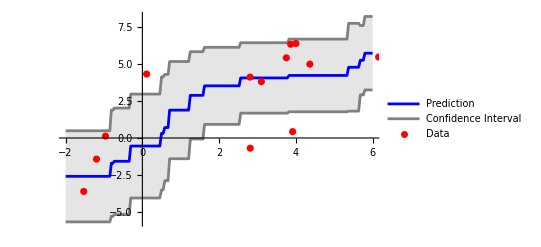

```mathematica
Show[Plot[{p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,-2,6},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},
Exclusions->False,
PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"Data"}]]
```

```mathematica
p
```

PredictorFunction[…]

```mathematica
x
```

x

```mathematica
n=Nearest[dangle]
```

NearestFunction[…]

```mathematica
Table[dangle->listofpixels]
```

```mathematica
Show[ListPlot[{n},PlotMarkers->{{Automatic,Tiny}},AspectRatio->1]]
```

-Graphics-

```mathematica
Show[ListPlot[{listofpixels},PlotMarkers->{{Automatic,Tiny}},AspectRatio->1],ListPlot[{dangle},PlotMarkers->{{Automatic,Medium}},AspectRatio->1]]
```

-Graphics-

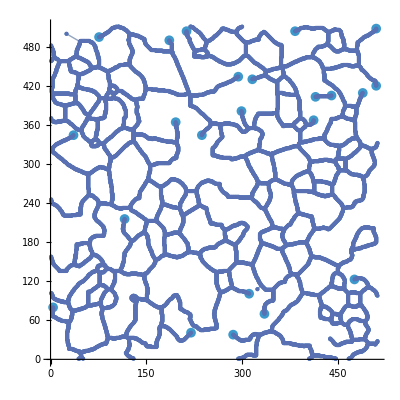

```mathematica
Show[ListPlot[{listofpixels},PlotMarkers->{{Automatic,Tiny}},AspectRatio->1],ListPlot[{dangle},PlotMarkers->{{Automatic,Medium}},AspectRatio->1],
NearestNeighborGraph[listofpixels]]
```